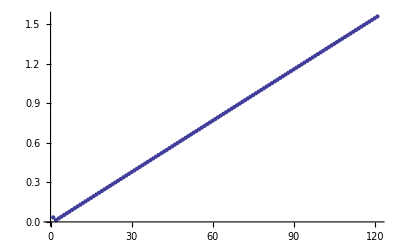

```mathematica
cons = 2 10^-3;
Clear [u];
r =.267;
func = NDSolve[{D[u[t,x, y],t]==cons (D[u[t,x, y],x,x]+D[u[t,x,y],y,y] ),u[0,x,y]==0,u[t,x,0]==r t,u[t,0,y]==r t,u[t,x,9]==r t, u[t,9,y]==r t },u,{t,0,12},{x,0,9},{y,0,9}];
Manipulate[Plot3D[Evaluate[u[2,x,y]/.func/.t -> taub],{x,0,9},{y,0,9},PlotRange->All], {taub,0,12}]
Clear [data];
Do[data[tsub]=Table[Evaluate[u[t,x,y] /.func/.t -> tsub/10], {x,0,9,1}, {y,0,9,1}],{tsub,0,120}];
dev=ConstantArray[0,{121,1}];
Do[newdata[i]=Flatten[data[i]],{i,0,120}]
Do[dev[[f]] = StandardDeviation[newdata[f]],{f,0,120}]
Table[dev[[i]],{i,0,120}];
ListPlot[{Table[dev[[i]],{i,0,120}]}]
```